# Stop Compton Scattering

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 1 diagram

> Top. 4 aebf/cfde/ef.m, 1 diagram



```mathematica
topo1=CreateTopologies[0,2->2];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

Excluding 0 Generic, 31 Classes, and 74 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 31 Classes, and 74 Particles fields

Restoring 18 field point(s)

in total: 3 Particles insertions

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 1 diagram

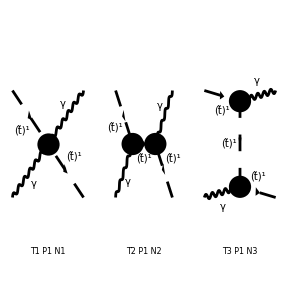

```mathematica
diag1=InsertFields[topo1,{S[13,{1,3}],V[1]}->{V[1],S[13,{1,3}]},InsertionLevel->{Particles},Model->"MSSM",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[13,{2,3}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral]
squ=SquaredME[amp];

(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)

(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/3;

(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matrix = PolarizationSum[squ,GaugeTerms->False]/2;  (*Asserting gauge invariance! *)

FullSimplify[matrix]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp((S(13,{1,3,Col1}) | k(1) | MSf(1,3,3) | {(2 Charge)/3,(2 ColorCharge)/(√3)}
V(1) | k(2) | 0 | {})→(V(1) | k(3) | 0 | {}
S(13,{1,3,Col4}) | k(4) | MSf(1,3,3) | {(2 Charge)/3,(2 ColorCharge)/(√3)}))(π Alfa Mat(SUN1) ((32 Pair5)/9-64/9 (Pair1 Pair2 Den(S,MSf2(1,3,3))+Pair3 Pair4 Den(T,MSf2(1,3,3)))))

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-3.frm

running FORM...

ok

1024/81 π^2 Alfa2 Sub4

#### Check divergent piece

```mathematica
UVDivergentPart[amp]
divergence=%[[1]]
```

Amp((S(13,{1,3,Col1}) | k(1) | MSf(1,3,3) | {(2 Charge)/3,(2 ColorCharge)/(√3)}
V(1) | k(2) | 0 | {})→(V(1) | k(3) | 0 | {}
S(13,{1,3,Col4}) | k(4) | MSf(1,3,3) | {(2 Charge)/3,(2 ColorCharge)/(√3)}))(0)

0

#### Prepare for looptools

Note: polarization sum auto squares the matrix element - also divide by colour and polarization factors

```mathematica
mat=(1/2)*(1/3)PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify
```

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-3.frm

running FORM...

ok

1024/81 π^2 Alfa2 (Den(S,MSf2(1,3,3)) (Den(T,MSf2(1,3,3)) (-3 U MSf2(1,3,3)+3 (MSf2(1,3,3))^2+S (T+U)+T U+U^2)-2 MSf2(1,3,3))+2 S MSf2(1,3,3) (Den(S,MSf2(1,3,3)))^2+2 MSf2(1,3,3) Den(T,MSf2(1,3,3)) (T Den(T,MSf2(1,3,3))-1))

## Numerical Evaluation

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=mat//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
feynArtsResult =MyMatrixElement[250,10000,0,250,-0.1008,1.47]
```

(π^2 ((T (S+U-125000)+(S-187500) U+U^2+19531250000)/((S-62500) (T-62500))+(125000 S)/(S-62500)^2+7812500000/(T-62500)^2))/1296

```mathematica
otherFeynResult = matrix//.Subexpr[]//.Abbr[]//.VALUES[250,10000,0,250,-0.1008,1.47]//Simplify
```

(π^2 (-(187500 (U-62500))/((S-62500) (T-62500))+(((S+U) (T+U))/(T-62500)-125000)/(S-62500)+125000 (S/(S-62500)^2+62500/(T-62500)^2)))/1296

```mathematica
FullSimplify[feynArtsResult == otherFeynResult,Assumptions->{S+T+U==2*250^2}]
```

True

## Calculate S, T, and U

```mathematica
ω2 = ω/(1 + (ω/m)(1-Cos[θ]))
```

ω/((ω (1-cos(θ)))/m+1)

```mathematica
ePrime = Sqrt[m^2 + ω2^2]
```

√(m^2+ω^2/((ω (1-cos(θ)))/m+1)^2)

```mathematica
s = 2*m*ω+m^2
t = -2*m*ePrime + 2*m^2
u = -2*m*ω2 + m^2
```

m^2+2 m ω

2 m^2-2 m √(m^2+ω^2/((ω (1-cos(θ)))/m+1)^2)

m^2-(2 m ω)/((ω (1-cos(θ)))/m+1)

```mathematica
snum =s/. m-> 250 /. ω->5/.θ-> 0.1
tnum = t/. m-> 250 /. ω->5/.θ-> 0.1
unum =u/. m-> 250 /. ω->5/.θ-> 0.1
```

65000

-24.9925

60000.2

```mathematica
Sqrt[(snum+tnum+unum)/2]
```

249.975

```mathematica
myCalc = (32/81)*(Alfa2*16*Pi^2)*(m^4(1/(m*ω)^2 +1/(m*ω2)^2) -(m*ePrime)^2/((m*ω)(m*ω2))+4-2(m*ePrime)/(m*ω)^2+2(m*ePrime)/(m*ω2)^2)
```

512/81 π^2 Alfa2 (-((m^2+ω^2/((ω (1-cos(θ)))/m+1)^2) ((ω (1-cos(θ)))/m+1))/ω^2+(2 √(m^2+ω^2/((ω (1-cos(θ)))/m+1)^2) ((ω (1-cos(θ)))/m+1)^2)/(m ω^2)-(2 √(m^2+ω^2/((ω (1-cos(θ)))/m+1)^2))/(m ω^2)+m^4 (((ω (1-cos(θ)))/m+1)^2/(m^2 ω^2)+1/(m^2 ω^2))+4)

```mathematica
myCalcNum = myCalc/. m-> 250 /. ω->5/.θ-> 0.1/.Alfa2->(1/128)^2
```

9.53167

```mathematica
feynArtsResultNum = feynArtsResult /.S-> snum/.T->tnum/.U->unum
```

9.14643

```mathematica
otherFeynResultNum = otherFeynResult/.S-> snum/.T->tnum/.U->unum
```

9.14643

```mathematica
myCalcNum/feynArtsResultNum
```

1.04212